```mathematica
(*PSOB*)
```

```mathematica
PSO[f_,dim_,popsize_,interval_,generationNum_]:=Module[{},
(*Initialization*)

G=RandomReal[interval,{popsize,dim}];
w=0.7;
c1=c2=1.49618;
v=Table[Table[0,dim],popsize];
pBest=G;
x=G;
generationBestSolutionVector={};



(*PSOB algorithm*)
For[n=1,n<=generationNum,n++,

pBestSolutions=Table[f[pBest[[a]]],{a,popsize}];
(*create neighborhood list*)
solutionNeighborhoods=Table[Table[pBestSolutions[[j]],{j,i-2,i+2}],{i,3,popsize-2}];
firstElement=Join[{pBestSolutions[[-2]],pBestSolutions[[-1]]},pBestSolutions[[1;;3]]];
secondElement=Join[{pBestSolutions[[-1]]},pBestSolutions[[1;;4]]];
lastElement=Join[pBestSolutions[[1;;2]],pBestSolutions[[popsize-2;;popsize]]];
secondLastElement=Join[{pBestSolutions[[1]]},pBestSolutions[[popsize-3;;popsize]]];
solutionNeighborhoods=Join[{firstElement},{secondElement},solutionNeighborhoods,{secondLastElement},{lastElement}];

(*get lBests from pBest*)
lBestSolutions=Min@#&/@solutionNeighborhoods;

lBests=pBest[[First@Flatten@Position[pBestSolutions,#]]]&/@lBestSolutions;

generationBestSolution=Min@lBestSolutions;
AppendTo[generationBestSolutionVector,generationBestSolution];





(*manipulate individuals*)

For[i=1,i<=popsize,i++,

For[j=1,j<=dim,j++,

(*get v*)
v[[i]][[j]]=w*v[[i]][[j]]+c1*RandomReal[1]*(pBest[[i]][[j]]-x[[i]][[j]])+c2*RandomReal[1]*(lBests[[i]][[j]]-x[[i]][[j]]);
(*limit v less than 20%*interval*)

If[v[[i]][[j]]>0.2*(interval[[2]]-interval[[1]]),v[[i]][[j]]=0.2*(interval[[2]]-interval[[1]])];
(*update x*)

x[[i]][[j]]=x[[i]][[j]]+v[[i]][[j]];

(*limit x inside the interval<-500,500>*)

If[x[[i]][[j]]>interval[[2]],x[[i]][[j]]=interval[[2]],If[x[[i]][[j]]<interval[[1]],x[[i]][[j]]=interval[[1]]]];


];
(*update pBest*)

If[f[x[[i]]]<pBestSolutions[[i]],pBest[[i]]=x[[i]]];

]

];
Return[generationBestSolutionVector]
]
```

```mathematica
(*SPHERE FUNCTION*)
sphere[x_]:=Module[
{},Sum[(x[[i]])^2,{i,Length@x}]]
```

```mathematica
(*SUM OF DIFFERENT POWERS FUNCTION*)
```

```mathematica
SDP[x_]:=Module[{l=Length@x},Sum[Abs[x[[i]]]^(i+1),{i,l}]]
```

```mathematica
(*SUM SQUARES FUNCTION*)
```

```mathematica
SS[x_]:=Module[{l=Length@x},Sum[i*(x[[i]]^2),{i,l}]]
```

```mathematica
(*TRID FUNCTION*)
```

```mathematica
Trid[x_]:=Module[{l=Length@x},Sum[(x[[i]]-1)^2,{i,l}]-Sum[x[[i]]*x[[i-1]],{i,2,l}]]
```

```mathematica
(*ROTATED HYPER-ELLIPSOID FUNCTION*)
```

```mathematica
RHE[x_]:=Module[{l=Length@x},Sum[Sum[x[[j]]^2,{j,i}],{i,l}]]
```

```mathematica
(*Convergence graphs*)
```

```mathematica
PSO[sphere,5,10,{-500,500},100]
```

{166547.,85343.7,25248.7,14730.3,14730.3,14730.3,4048.06,4048.06,2460.08,2421.65,2421.65,2421.65,2165.06,2165.06,1845.89,1173.7,1173.7,1173.7,1173.7,1148.47,754.473,697.765,697.765,697.765,697.765,697.765,559.08,559.08,161.484,161.484,161.484,149.83,141.375,141.375,84.1519,60.2465,60.2465,60.2465,60.2465,38.4803,6.33842,6.33842,6.33842,6.33842,6.33842,2.62622,2.62622,2.62622,2.62622,2.48726,2.48726,2.48726,2.48726,2.48726,1.91716,1.91716,1.9079,1.9079,1.18036,1.18036,1.18036,0.353716,0.353716,0.353716,0.353716,0.353716,0.353716,0.353716,0.353716,0.278336,0.278336,0.256303,0.201762,0.201762,0.201762,0.201762,0.100984,0.100984,0.100984,0.100984,0.0179375,0.0179375,0.0179375,0.0107326,0.0107326,0.0107326,0.0107326,0.0107326,0.00264303,0.00264303,0.00264303,0.00264303,0.00264303,0.00264303,0.00264303,0.00226045,0.000427561,0.000427561,0.000427561,0.000427561}

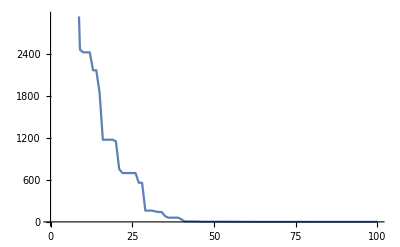

```mathematica
ListLinePlot@generationBestSolutionVector
```

```mathematica
PSO[SDP,5,10,{-500,500},100]
```

{1.29379×10^12,3.25798×10^9,6.18016×10^7,6.18016×10^7,6.18016×10^7,6.18016×10^7,6.18016×10^7,6.18016×10^7,6.18016×10^7,5.38526×10^7,5.38526×10^7,5.38526×10^7,5.38526×10^7,5.38526×10^7,5.38526×10^7,5.38526×10^7,2.18024×10^7,1.84698×10^7,1.84698×10^7,1.5827×10^7,1.04451×10^6,394753.,394753.,28428.9,28428.9,28428.9,28428.9,28428.9,28428.9,28428.9,28428.9,28428.9,8774.22,7960.7,7960.7,7960.7,7874.7,7874.7,7874.7,7774.19,7736.3,7667.61,7667.61,7667.61,5945.01,4232.65,1136.42,1136.42,1136.42,721.398,388.52,388.52,388.52,388.52,166.592,56.1531,38.4065,38.4065,38.4065,38.4065,28.7863,28.7863,28.7863,28.7863,22.0627,22.0627,1.7421,0.34138,0.34138,0.34138,0.34138,0.34138,0.34138,0.34138,0.2415,0.2415,0.231216,0.231216,0.11845,0.11845,0.11845,0.11845,0.11845,0.11845,0.0430662,0.0430662,0.0430662,0.0202103,0.0122794,0.00493125,0.00493125,0.00493125,0.00137948,0.000967203,0.000967203,0.000967203,0.000561314,0.000561314,0.000561314,0.000561314}

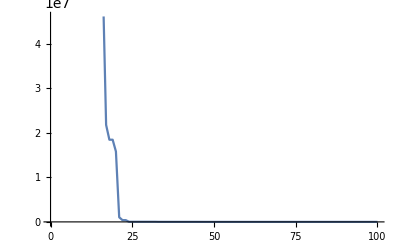

```mathematica
ListLinePlot@generationBestSolutionVector
```

```mathematica
PSO[SS,5,10,{-500,500},100]
```

{276814.,162116.,60739.9,60739.9,56887.7,54718.7,30117.8,30117.8,30117.8,30117.8,30117.8,30117.8,24770.6,11269.3,8984.74,8984.74,3767.01,3767.01,3767.01,3715.45,3715.45,3715.45,2846.87,2290.02,1030.74,1030.74,775.787,427.514,427.514,427.514,427.514,427.514,427.514,427.514,192.384,115.48,115.48,75.7288,75.7288,75.7288,73.8509,63.0083,61.2312,52.4162,47.2434,47.2434,47.2434,36.8789,27.0221,22.5538,16.6391,12.856,12.856,12.856,11.8296,11.8296,7.29148,7.29148,7.29148,7.13509,7.13509,4.28045,3.67767,3.67767,2.46651,2.36619,2.36619,2.32963,2.18913,2.18913,1.06886,1.06886,1.06886,0.785892,0.520522,0.520522,0.520522,0.31504,0.31504,0.31504,0.31504,0.0463741,0.0463741,0.0463741,0.0463741,0.0463741,0.0463741,0.0463741,0.0463741,0.042027,0.0360883,0.0360883,0.0281777,0.00313097,0.00313097,0.00152211,0.00152211,0.00152211,0.00152211,0.00152211}

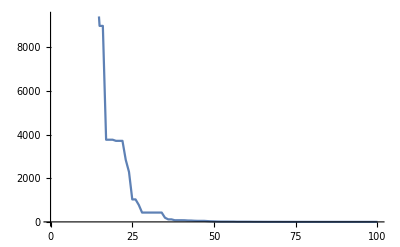

```mathematica
ListLinePlot@generationBestSolutionVector
```

```mathematica
PSO[Trid,5,10,{-500,500},100]
```

{53816.6,17382.1,17382.1,17382.1,11115.3,11115.3,11115.3,11115.3,10452.9,5030.08,5030.08,5030.08,5030.08,3044.97,2462.05,2462.05,1530.94,1530.94,798.79,487.678,487.678,487.678,214.954,214.954,214.954,214.954,214.954,214.954,206.351,127.583,127.583,85.1033,37.3943,26.7391,26.7391,24.2159,22.7253,12.3039,12.3039,12.3039,9.66355,7.98932,5.49681,5.04353,5.04353,5.04353,5.04353,5.04353,-11.878,-11.878,-15.2541,-15.2541,-15.2541,-15.2541,-15.2541,-17.944,-17.944,-18.6661,-19.8868,-19.8868,-19.8868,-19.9788,-19.9788,-20.2883,-20.2883,-21.8929,-21.8929,-22.9957,-24.1039,-25.8013,-27.8536,-28.4275,-28.4275,-28.5084,-28.5084,-28.5084,-28.5084,-28.8695,-28.8695,-28.8695,-29.0473,-29.0473,-29.0473,-29.0473,-29.0473,-29.0473,-29.0473,-29.1409,-29.1409,-29.1409,-29.1409,-29.1409,-29.1409,-29.1446,-29.1446,-29.1446,-29.1446,-29.1703,-29.1822,-29.2141}

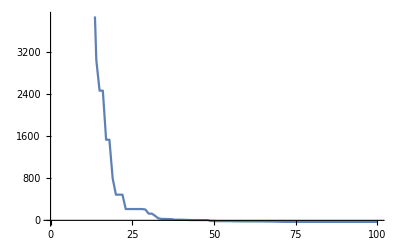

```mathematica
ListLinePlot@generationBestSolutionVector
```

```mathematica
PSO[RHE,5,10,{-500,500},100]
```

{297271.,297271.,142223.,77904.9,52434.3,41336.5,41336.5,41336.5,41336.5,31860.9,31860.9,16989.7,10433.7,952.44,952.44,952.44,952.44,674.846,674.846,674.846,674.846,674.846,674.846,674.846,457.083,457.083,445.644,411.134,411.134,411.134,302.036,226.471,226.471,226.471,224.394,194.341,194.339,149.083,78.7029,78.7029,78.7029,78.7029,38.899,38.899,38.899,38.899,28.1743,28.1743,14.37,14.37,14.37,14.37,14.37,10.4936,10.4936,10.4936,10.4936,10.4936,7.70185,2.97119,2.97119,2.97119,2.97119,2.97119,2.97119,2.97119,2.94599,2.94599,2.28602,1.94642,1.94642,1.94642,1.54188,0.956253,0.857295,0.83615,0.83615,0.83615,0.675898,0.649176,0.649176,0.609287,0.521278,0.451554,0.223727,0.223727,0.217592,0.184199,0.166113,0.15945,0.155373,0.152617,0.152617,0.152579,0.152579,0.0605016,0.0270043,0.0270043,0.0270043,0.0223548}

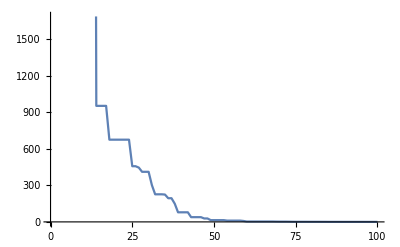

```mathematica
ListLinePlot@generationBestSolutionVector
```